## Transmittance PEDOT:PSS ~From Moritz

```mathematica
(*Set graphics style*) Needs["CustomTicks`"];
ticksx=LinTicks[100,1200,100,4,MajorTickLength->{.0,-0.025},MinorTickLength->{.0,-0.015},MajorTickStyle->{Thick,GrayLevel[0.1]},MinorTickStyle->{Thick,GrayLevel[0.1]}];
ticksy=LinTicks[0,1,0.2,2,MajorTickLength->{.0,-0.025},MinorTickLength->{.0,-0.015},MajorTickStyle->{Thick,GrayLevel[0.1]},MinorTickStyle->{Thick,GrayLevel[0.3]}];
```

Get::noopen: Cannot open CustomTicks`.

Needs::nocont: Context CustomTicks` was not created when Needs was evaluated.

```mathematica
NotebookDirectory[]
```

P:\Engineering\SolarField\Talia\Code\

```mathematica
SetDirectory[NotebookDirectory["P:\\Engineering\\SolarField\\Talia\\Data\\UVVis\\Oct25th\\"]]
```

SetDirectory::fstr: File specification NotebookDirectory[P:\Engineering\SolarField\Talia\Data\UVVis\Oct25th\] is not a string of one or more characters.

SetDirectory[NotebookDirectory[P:\Engineering\SolarField\Talia\Data\UVVis\Oct25th\]]

```mathematica
(*Import all datafiles, one for each Sample*)
(*drop first item, the title and switch the separator from \t to , *)
Sample1=Drop[Import["Sample1.1.Sample.Raw.csv", "Table", FieldSeparators->"\\t"],1]; 
Sample2=Import["Sample2.Sample.Raw.csv", "Table", FieldSeparators->"\\t"];
Sample3=Import["Sample3.Sample.Raw.csv", "Table", FieldSeparators->"\\t"];
Sample4=Import["Sample4.Sample.Raw.csv", "Table", FieldSeparators->"\\t"];
Sample5=Import["Sample5.Sample.Raw.csv", "Table", FieldSeparators->"\\t"];
Sample6=Import["Sample6.Sample.Raw.csv", "Table", FieldSeparators->"\\t"];
```

SetDirectory::fstr: File specification NotebookDirectory[P:\Engineering\SolarField\Talia\Data\UV-Vis\Oct 25th\] is not a string of one or more characters.

Import::nffil: File not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,1].

Import::nffil: File not found during Import.

```mathematica
(*Here I import generalized data into one long sheet*)Data=Table[Import["Sample*.Sample.Raw.csv","Table", FieldSeparators->"\\t"],6];

(*Now I want to split that long list into n smaller ones where n=6*)
StringSplit["Data", "n"];
```

```mathematica
(*full range of spectra*)
PlotFigure = ListPlot[{Sample1, Sample2, Sample3, Sample4, Sample5, Sample6},

PlotRange->{{350,1200},{0,0.4}},Joined->True,Frame->True,FrameStyle->Directive[GrayLevel[0.1],Thickness[0.005]],

FrameLabel->{"Wavelength (nm)","Absorbance (OD)"},

LabelStyle->{FontSize->12,FontFamily->"Helvetica",GrayLevel[0.1],Bold},

PlotLegends->Placed[{"CIGS","CdTe", "Polysi", "IBCSi", "HITSi", "CIGSm"},{1,0.6}],

ImageSize->400,AspectRatio->0.6]
```

-Graphics-

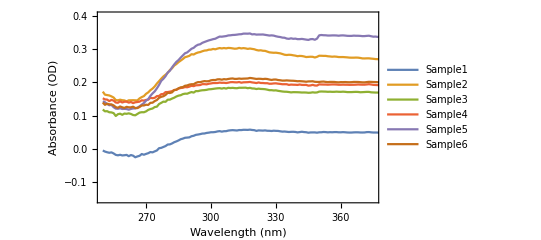

```mathematica
(*Here I try plotting the raw data without normalization; 250-350 nm*)
PlotFigure1 = ListPlot[{Sample1, Sample2, Sample3, Sample4, Sample5, Sample6},

PlotRange->{{250,375},{-0.15,0.4}},Joined->True,Frame->True,FrameStyle->Directive[GrayLevel[0.1],Thickness[0.005]],

FrameLabel->{"Wavelength (nm)","Absorbance (OD)"},

LabelStyle->{FontSize->16,FontFamily->"Helvetica",GrayLevel[0.1],Bold},

PlotLegends->Placed[{"Sample1","Sample2", "Sample3", "Sample4", "Sample5", "Sample6"},{0.8,0.42}],

ImageSize->400,AspectRatio->0.6]
```

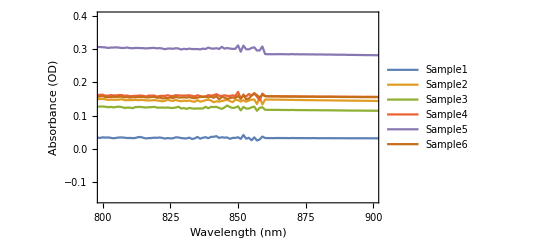

```mathematica
(*800-900nm*)PlotFigure2 = ListPlot[{Sample1, Sample2, Sample3, Sample4, Sample5, Sample6},

PlotRange->{{800,900},{-0.15,0.4}},Joined->True,Frame->True,FrameStyle->Directive[GrayLevel[0.1],Thickness[0.005]],

FrameLabel->{"Wavelength (nm)","Absorbance (OD)"},

LabelStyle->{FontSize->10,FontFamily->"Helvetica",GrayLevel[0.1],Bold},

PlotLegends->Placed[{"Sample1","Sample2", "Sample3", "Sample4", "Sample5", "Sample6"},{0.2,0.2}],

ImageSize->400,AspectRatio->0.6]
```

### Export Figures

```mathematica
SetDirectory[NotebookDirectory[ ]]
```

```mathematica
export[name_,figure_]:=Export[name,Magnify[figure,2],Background->White];
```